```mathematica
listAlpha={}
listBeta={}
foo[n_]:=
Module[
{
iterator=1,
listA={},
listB={}
},
While[
iterator<1000,
If[
Mod[iterator,6]==0,
AppendTo[listA,iterator];
If[RandomInteger[{1,6}]==6,
AppendTo[listB,iterator]
],
If[RandomInteger[{1,6}]==6,
AppendTo[listB,iterator]
]
];
iterator=iterator+1
];
{listA, listB, Length@listA,Length@listB}
]
```

{}

{}

```mathematica
Mod[4,2]
```

0

```mathematica
RandomInteger[{1,6}]
```

6

```mathematica
listA
```

{}

```mathematica
foo
```

```mathematica
listA
```

{}

```mathematica
results:=

Module[
{
iterator=1,
sentinel={},
listOne={},
listTwo={}

},
While[
iterator<100,
sentinel=foo[1];
AppendTo[listOne,sentinel[[3]]];
AppendTo[listTwo,sentinel[[4]]];
iterator=iterator+1
];
{listOne,listTwo}
]
```

```mathematica
results
```

{{166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166,166},{182,153,174,158,179,175,167,181,175,163,169,164,155,165,169,163,167,169,176,156,164,157,163,154,155,173,169,181,170,173,178,144,184,163,146,158,163,185,183,153,160,143,149,162,178,165,181,184,167,166,182,179,153,153,156,169,179,175,162,163,171,155,171,187,171,156,146,149,175,171,177,150,168,167,175,171,178,165,166,165,180,165,165,158,193,169,151,170,162,158,153,159,161,161,143,167,154,178,149}}

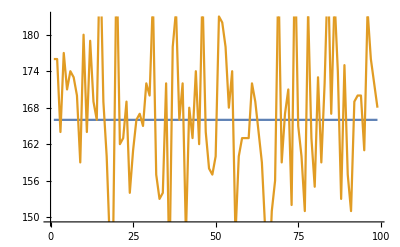

```mathematica
ListLinePlot@results
```

```mathematica
Module[
{
iterator=1,
listA={},
listB={}
},
While[
iterator<10,
Print["foo"];
iterator=iterator+1
]
]
```

foo

foo

foo

«6 more identical outputs»

```mathematica
foo
```

foo

```mathematica
Four
```

```mathematica
integrateThis:=ListFourierSequenceTransform[results[[2]],t]
```

```mathematica
Abs@N@Integrate[integrateThis,{t,0,100}]
```

14008.7

```mathematica
resultsB:=

Module[
{
iterator=1,
sentinel={},
listOne={},
listTwo={}

},
While[
iterator<100,
sentinel=foo[1];
AppendTo[listOne,sentinel[[3]]-sentinel[[4]]];
iterator=iterator+1
];
{listOne,Total@listTwo}
]
```

```mathematica
resultsB
```

{{-17,-7,-2,12,11,20,-2,-5,-5,13,-8,8,-7,12,-13,-5,-6,-3,-16,8,2,-5,-5,-10,-3,-1,11,2,-4,-6,-6,-6,-22,7,22,14,-25,-7,18,3,2,-3,-4,2,-11,0,-4,-20,-1,25,8,2,-2,3,7,14,1,7,14,-11,-15,-23,-9,26,-4,-9,-8,14,24,9,-10,-8,7,12,3,6,-5,-6,-12,12,-17,5,-10,8,-10,9,5,-9,12,-13,-4,-18,1,2,14,-17,13,7,12},0}